# Marcus rate expression for Onodera solvent

## Numerical integration of the flux

## Constants

### Unit conversions

```mathematica
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
fs2ps=10^-3;
ps2au=1/au2ps;
```

### Universal constants

```mathematica
hbar=1;
kb=3.16683 10^-6;
```

## Dielectric function

```mathematica
ϵO[ω_]:=ϵi+(ϵ0-ϵi)/((1-ⅈ ω τD)(1-ⅈ ω τO));
```

```mathematica
imϵO[ω_]:=(ω (τD+τO)(ϵ0-ϵi))/((1+ω^2 τD^2)(1+ω^2 τO^2));
```

```mathematica
reϵO[ω_]:=ϵi+((ϵ0-ϵi)(1 - ω^2 τO τD))/((1+ω^2 τD^2)(1+ ω^2 τO^2));
```

```mathematica
ϵOabs2[ω_]:=(reϵO[ω])^2+(imϵO[ω])^2;
```

```mathematica
ξ[ω_]:=imϵO[ω]/ϵOabs2[ω];
```

```mathematica
FullSimplify[ξ[ω]]
```

((ϵ0-ϵi) (τD+τO) ω)/(ϵ0^2+ϵi (-2 ϵ0 τD τO+ϵi (τD+τO)^2) ω^2+ϵi^2 τD^2 τO^2 ω^4)

High-T expansion (x=βℏω)

```mathematica
Series[(Cosh[1/2 x-(ⅈ x Abs[t])/(β ℏ)]-Cosh[1/2 x])/Sinh[1/2 x],{x,0,2}]
```

-(ⅈ (β ℏ Abs[t]-ⅈ Abs[t]^2) x)/(β^2 ℏ^2)+O[x]^3

Full flux (before integration over ω):

```mathematica
g[ω_] =-(f0 λ)/(4 π^2 ℏ)1/ω^2 ξ[ω]((ⅈ β ℏ Abs[t]+t^2) ω)/(β ℏ);
```

```mathematica
G[ω_] =-(f0 λ)/(4 π^2 ℏ)((ϵ0-ϵi) (τD+τO))/(β ℏ)1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) ω^2+ϵi^2 τD^2 τO^2 ω^4)(ⅈ β ℏ Abs[t]+t^2);
```

```mathematica
G[x]-g[x]//FullSimplify
```

0

```mathematica
roots=Solve[ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z+ϵi^2 τD^2 τO^2 z^2==0,z]
```

{{z→1/(2 ϵi^2 τD^2 τO^2)(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2-√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))},{z→1/(2 ϵi^2 τD^2 τO^2)(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2+√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))}}

```mathematica
rootsNum[τO_,τD_,ϵi_,ϵ0_]:=Solve[ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z^2+ϵi^2 τD^2 τO^2 z^4==0,z];
```

```mathematica
Z1=roots⟦1,1,2⟧
```

(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2-√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2)

```mathematica
Z2=roots⟦2,1,2⟧
```

(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2+√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2)

```mathematica
z1root[τO_,τD_,ϵi_,ϵ0_]:=1/(2 ϵi^2 τD^2 τO^2)(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2-√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2));
```

```mathematica
z2root[τO_,τD_,ϵi_,ϵ0_]:=1/(2 ϵi^2 τD^2 τO^2)(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2+√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2));
```

```mathematica
Limit[Z1,{τO->0},Assumptions->{ϵi>0,ϵ0>0,τD>0},Direction->-1]
```

{-∞}

```mathematica
Limit[Z2,{τO->0},Assumptions->{ϵi>0,ϵ0>0,τD>0},Direction->-1]
```

{-ϵ0^2/(ϵi^2 τD^2)}

```mathematica
Integrate[1/((ω^2-z1)(ω^2-z2)),{ω,-∞,∞}]
```

ConditionalExpression[-(ⅈ π)/(z1 √z2+√z1 z2),Im[√z2]>0&&Im[√z1]>0]

```mathematica
omegaInum[τO_,τD_,ϵi_,ϵ0_]:=Module[{},
NIntegrate[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) ω^2+ϵi^2 τD^2 τO^2 ω^4),{ω,-∞,∞},MinRecursion->10,MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->∞]
];
```

```mathematica
omegaIana[τO_,τD_,ϵi_,ϵ0_]:=Module[{z1,z2,term1,term2,result},
If[τO==0,
result=N[π,30]/(ϵ0 ϵi τD),
z1=(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2-√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2);
z2=(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2+√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2);
If[Im[√z1]==0,Print["Real root z1... No analytical solution!"];Abort[]];
If[Im[√z2]==0,Print["Real root z2... No analytical solution!"];Abort[]];
If[Im[√z1]>0,term1=1/(√z1(z1-z2)),term1=1/(√z1(z2-z1))];
If[Im[√z2]>0,term2=1/(√z2(z2-z1)),term2=1/(√z2(z1-z2))];
result=ⅈ N[π,30](term1+term2)];
result
];
```

```mathematica
SetAccuracy[π,60]
```

3.14159265358979323846264338327950288419716939937510582097494

```mathematica
omegaIanaR[τO_,τD_,ϵi_,ϵ0_]:=Module[{z1,z2,res1,res2,result},
If[τO==0,
result=π/(ϵ0 ϵi τD),
z1=(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2-√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2);
z2=(-ϵi^2 τD^2+2 ϵ0 ϵi τD τO-2 ϵi^2 τD τO-ϵi^2 τO^2+√(-4 ϵ0^2 ϵi^2 τD^2 τO^2+(ϵi^2 τD^2-2 ϵ0 ϵi τD τO+2 ϵi^2 τD τO+ϵi^2 τO^2)^2))/(2 ϵi^2 τD^2 τO^2);
If[Im[√z1]==0,Print["Real root z1... No analytical solution!"];Abort[]];
If[Im[√z2]==0,Print["Real root z2... No analytical solution!"];Abort[]];
If[Im[√z1]>0,res1=Residue[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z^2+ϵi^2 τD^2 τO^2 z^4),{z,√z1}],res1=Residue[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z^2+ϵi^2 τD^2 τO^2 z^4),{z,-√z1}]];
If[Im[√z2]>0,res2=Residue[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z^2+ϵi^2 τD^2 τO^2 z^4),{z,√z2}],res2=Residue[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) z^2+ϵi^2 τD^2 τO^2 z^4),{z,-√z2}]];
result=2π ⅈ (res1+res2)];
result
];
```

```mathematica
omegaInum[0.5,8.5`30,1.75`30,79.1`30]
```

0.00252169658948069932021763141745

```mathematica
omegaIana[0.08`30,8.5`30,1.75`30,79.1`30]
```

0.00374577748989190851709348325+0. ⅈ

```mathematica
omegaIanaR[0.5`10,8.5`30,1.75`30,79.1`30]
```

0.0025217+0. ⅈ

```mathematica
N[π,30]
```

3.14159265358979323846264338328

## ω-integrand

```mathematica
ωIntegrand[τO_,τD_,ϵi_,ϵ0_,ω_]:=1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) ω^2+ϵi^2 τD^2 τO^2 ω^4);
```

```mathematica
ωIntegrand[0,τD,ϵi,ϵ0,ω]
```

1/(ϵ0^2+ϵi^2 τD^2 ω^2)

```mathematica
Integrate[1/(ϵ0^2+ϵi^2 τD^2 ω^2),{ω,-∞,∞},Assumptions->{ϵi>0,ϵ0>0,τD>0}]
```

π/(ϵ0 ϵi τD)

```mathematica
eps0=79.1`20;
epsi=1.75`20;
tauO=0.025`20;
tauD=8.5`20;
```

```mathematica
Manipulate[Plot[ωIntegrand[τO,tauD,epsi,eps0,ω],{ω,-50,50},PlotRange->{0,1.5/eps0^2}],{τO,0,0.5}]
```

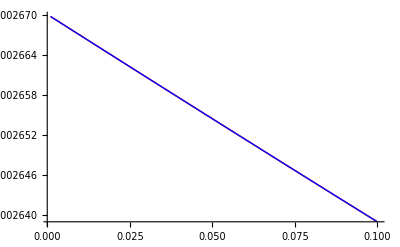

```mathematica
Plot[{omegaIanaR[τO,tauD,epsi,eps0],omegaInum[τO,tauD,epsi,eps0]},{τO,0.001`20,0.1`20},PlotRange->All,PlotStyle->{Red,Blue},WorkingPrecision->30]
```

```mathematica
Limit[omegaIanaR[x,tauD,epsi,eps0],x->0]
```

result$38751

## Flux

```mathematica
fluxOnoderaNum[G_, λ_, τO_,τD_,t_,ϵi_,ϵ0_,T_] := Module[{β,prefactor,z1,z2,hbar,f0,FI,term1,term2},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
f0 =  (4 π ϵ0 ϵi)/(ϵ0-ϵi);
prefactor=-(f0 λ(ϵ0-ϵi) (τD+τO))/(4 π^2 β hbar^2);
FI=NIntegrate[1/(ϵ0^2-ϵi (2 ϵ0 τD τO-ϵi (τD+τO)^2) ω^2+ϵi^2 τD^2 τO^2 ω^4),{ω,-∞,∞},MinRecursion->10,MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->∞];
Exp[-ⅈ/hbar(G+λ)t+ⅈ/hbar λ Abs[t]]*Exp[prefactor*FI*(t^2+ⅈ Abs[t] β hbar)]
];
```

```mathematica
fluxOnoderaAna[G_, λ_, τO_,τD_,t_,ϵi_,ϵ0_,T_] := Module[{β,prefactor,z1,z2,hbar,f0,FI,term1,term2},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
f0 =  (4 π ϵ0 ϵi)/(ϵ0-ϵi);
prefactor=-(f0 λ(ϵ0-ϵi) (τD+τO))/(4 π^2 β hbar^2);
FI=omegaIanaR[τO,τD,ϵi,ϵ0];
Exp[-ⅈ/hbar(G+λ)t+ⅈ/hbar λ Abs[t]]*Exp[prefactor*FI*(t^2+ⅈ Abs[t] β hbar)]
];
```

```mathematica
fluxOnoderaAna[-10,20,0.05`20,8.5`20,0,1.75`20,79.1`20,298]
```

1.+0. ⅈ

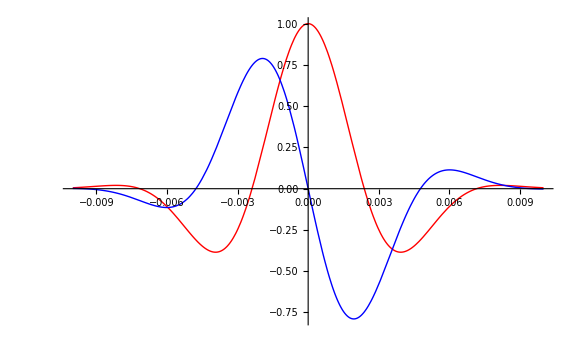

-Graphics-

```mathematica
eps0=79.1`20;
epsi=1.75`20;
λ=20.0;
dG=-10;
Temp=298;
tauO=0.025`20;
tauD=8.5`20;
Plot[{Re[fluxOnoderaAna[dG,λ,tauO,tauD,t,epsi,eps0,Temp]],Im[fluxOnoderaAna[dG,λ,tauO,tauD,t,epsi,eps0,Temp]]},{t,-0.01,0.01},PlotRange->All,PlotStyle->{Red,Blue},ImageSize->Large]
Plot[{Re[fluxOnoderaNum[dG,λ,tauO,tauD,t,epsi,eps0,Temp]],Im[fluxOnoderaAna[dG,λ,tauO,tauD,t,epsi,eps0,Temp]]},{t,-0.01,0.01},PlotRange->All,PlotStyle->{Red,Blue},ImageSize->Large]
```

## Nonadiabatic rate

```mathematica
Marcusrate[V_,G_,λ_,T_]:=Module[{β,hbar},
β=1/(kb T au2kcal);
hbar=au2kcal au2ps;
(2π)/hbar V^2 √(β/(4π λ))Exp[-β(G+λ)^2/(4λ)]
];
```

```mathematica
rateOnoderaNum[V_,G_,λ_,τO_,τD_,ϵi_,ϵ0_,T_] := Module[{β,hbar,integral},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
integral = NIntegrate[Re[fluxOnoderaNum[G,λ,τO,τD,t,ϵi,ϵ0,T]],{t,-∞,∞},WorkingPrecision->30];
V^2/hbar^2 Re[integral] 
];
```

```mathematica
rateOnoderaAna[V_,G_,λ_,τO_,τD_,ϵi_,ϵ0_,T_] := Module[{β,hbar,integral},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
integral = NIntegrate[Re[fluxOnoderaAna[G,λ,τO,τD,t,ϵi,ϵ0,T]],{t,-∞,∞},WorkingPrecision->30];
V^2/hbar^2 Re[integral] 
];
```

```mathematica
V=0.1;
Er=20.0;
dG=-10;
tauD=8.5`20;
Temp=298;
V = 0.1;
rateOnoderaNum[V,dG,Er,0,tauD,epsi,eps0,Temp]
rateOnoderaAna[V,dG,Er,0,tauD,epsi,eps0,Temp]
Marcusrate[V,dG,Er,Temp]
```

0.0411035

0.0411035

0.0411035

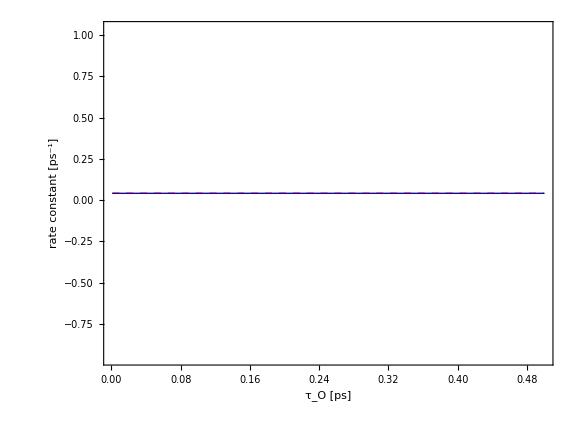

```mathematica
ListLinePlot[{Table[{τO,Marcusrate[V,dG,Er,Temp]},{τO,0.001`20,0.5`20,0.001`20}],Table[{τO,rateOnoderaAna[V,dG,Er,τO,tauD,epsi,eps0,Temp]},{τO,0.001`20,0.5`20,0.001`20}]},PlotRange->All,PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"τ_O [ps]","rate constant [ps^-1]"},AspectRatio->0.75,ImageSize->Large]
```